```mathematica
U[T_,λ4_,λ6_]:=((T-1)/(2))ϕ^2+(λ4/(4!))ϕ^6+(λ6/(6!))ϕ^6
```

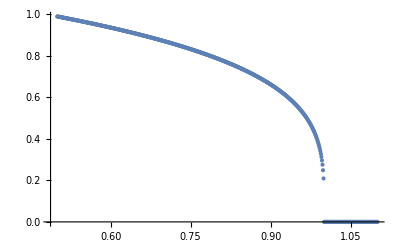

```mathematica
ListPlot[ParallelTable[{T,Abs[ϕ]/.NMinimize[U[T,2,3],ϕ][[2]]},{T,0.5,1.1,0.001}]]
```

```mathematica
D[Conjugate[ps],ps]
```

Conjugate'[ps]